```mathematica
f[x_]=Exp[-a^2(x-u)^2]
```

ⅇ^(-a^2 (-u+x)^2)

```mathematica
intf=Integrate[f[x],{x,0,1}]
```

(√π (Erf[a u]+Erf[a-a u]))/(2 a)

```mathematica
fp[x_]=D[f[x],x]
```

-2 a^2 ⅇ^(-a^2 (-u+x)^2) (-u+x)

```mathematica
fp1norm=2f[u]-f[0]-f[1]
```

2-ⅇ^(-a^2 (1-u)^2)-ⅇ^(-a^2 u^2)

```mathematica
fpp[x_]=Simplify[D[fp[x],x]]
```

ⅇ^(-a^2 (u-x)^2) (-2 a^2+4 a^4 (u-x)^2)

```mathematica
fppcase[x_]=fpp[x]/.{u->0, a->1}
```

ⅇ^(-x^2) (-2+4 x^2)

```mathematica
Maximize[Abs[fppcase[x]],x]
```

{2,{x→0}}

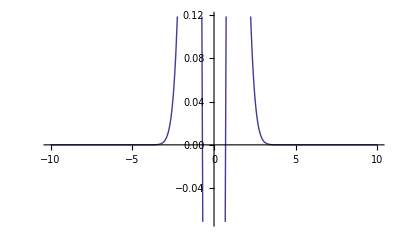

```mathematica
Plot[fppcase[x],{x,-10,10}]
```

```mathematica
Solve[fpp[x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(-√2+2 a u)/(2 a)},{x→(√2+2 a u)/(2 a)}}

```mathematica
fpinfnorm=Simplify[fp[(√2+2 a u)/(2 a)]]
```

-a √(2/ⅇ)

```mathematica
fpp1norm=2*fp[u-1/(Sqrt[2]a)]+-2*fp[u+1/(Sqrt[2]a)]-fp[0]+fp[1]
```

4 a √(2/ⅇ)-2 a^2 ⅇ^(-a^2 (1-u)^2) (1-u)-2 a^2 ⅇ^(-a^2 u^2) u

```mathematica
fppp[x_]=Simplify[D[fpp[x],x]]
```

4 a^4 ⅇ^(-a^2 (u-x)^2) (-3+2 a^2 (u-x)^2) (u-x)

```mathematica
4 a^4 ⅇ^(-a^2 (u-x)^2) (-3+2 a^2 (u-x)^2) (u-x)
```

4 a^4 ⅇ^(-a^2 (u-x)^2) (-3+2 a^2 (u-x)^2) (u-x)

```mathematica
Solve[fppp[x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→u},{x→(-√6+2 a u)/(2 a)},{x→(√6+2 a u)/(2 a)}}

```mathematica
fpp[u]
```

-2 a^2

```mathematica
fpp[(√6+2 a u)/(2 a)]
```

ⅇ^(-a^2 (u-(√6+2 a u)/(2 a))^2) (-2 a^2+4 a^4 (u-(√6+2 a u)/(2 a))^2)

```mathematica
Integrate[f[x],{x,0,y}]
```

(√π (Erf[a u]-Erf[a (u-y)]))/(2 a)